```mathematica
trialFunction:=Sech[beta x]^2
```

```mathematica
Integrate[trialFunction trialFunction n^2,{x,-∞,∞}]
```

ConditionalExpression[(4 n^2)/(3 beta),(ⅈ^(1/beta)∈ℝ||Im[ⅈ^(1/beta)]<0||Im[ⅈ^(1/beta)]>0)&&(Re[ⅈ^(1/beta)]==0||Re[ⅈ^(1/beta)]==1||Re[ⅈ^(1/beta)]≥1||Re[ⅈ^(1/beta)]≤0||ⅈ^(1/beta)∉ℝ)&&(ⅈ^(1/beta)≥1||Im[ⅈ^(1/beta)]<0||ⅈ^(1/beta)≤0||Im[ⅈ^(1/beta)]>0)&&Re[beta]>0]

```mathematica
Solve[(4 n^2)/(3 beta)==1,n]
```

{{n→-1/2 √3 √beta},{n→(√3 √beta)/2}}

```mathematica
Integrate[trialFunction (-1/2  D[D[trialFunction,x],x] + x^2/2 trialFunction),{x,-∞,∞}]
```

ConditionalExpression[(8 beta)/15+(-6+π^2)/(18 beta^3),(ⅈ^(1/beta)≥1||Im[ⅈ^(1/beta)]<0||ⅈ^(1/beta)≤0||Im[ⅈ^(1/beta)]>0)&&Re[beta]>0]

```mathematica
Solve[ D[3 beta /4((8 beta)/15+(-6+π^2)/(18 beta^3)),beta]==0,beta]
```

{{beta→-1/2 (1/3 (-30+5 π^2))^(1/4)},{beta→-1/2 ⅈ (1/3 (-30+5 π^2))^(1/4)},{beta→1/2 ⅈ (1/3 (-30+5 π^2))^(1/4)},{beta→1/2 (1/3 (-30+5 π^2))^(1/4)}}

```mathematica
N[(1/2 √3 √beta)^2((8 beta)/15+(-6+π^2)/(18 beta^3))/. beta->1/2 (1/3 (-30+5 π^2))^(1/4)]
```

0.507911

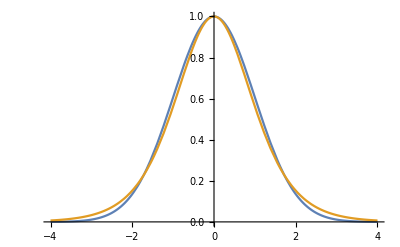

```mathematica
Plot[{Exp[-1/2 x^2],Sech[1/2 (1/3 (-30+5 π^2))^(1/4)x]^2},{x,-4,4}]
```